基本运算

```mathematica
2+5
```

7

```mathematica
2-5
```

-3

```mathematica
2*5
```

10

```mathematica
2/5
```

2/5

符号N

https://reference.wolfram.com/language/ref/N.html?q=N

```mathematica
N[(1+4)/2]
```

2.5

```mathematica
N[Sin[1]]
```

0.841471

```mathematica
N[Pi, 5]
```

3.1416

Set =

https://reference.wolfram.com/language/ref/Set.html

SetDelayed :=

https://reference.wolfram.com/language/ref/SetDelayed.html

```mathematica
a = 5
a + 3
```

5

8

ReplaceAll /.

https://reference.wolfram.com/language/ref/ReplaceAll.html

```mathematica
a + b
a + b/.a -> 12
```

5+b

12+b

```mathematica
a + b /. a -> 12 /. b -> x + y
```

12+x+y

```mathematica
a + b /. {a -> 12, b -> x+y}
```

12+x+y

ParametricPlot

https://reference.wolfram.com/language/ref/ParametricPlot.html?q=ParametricPlot

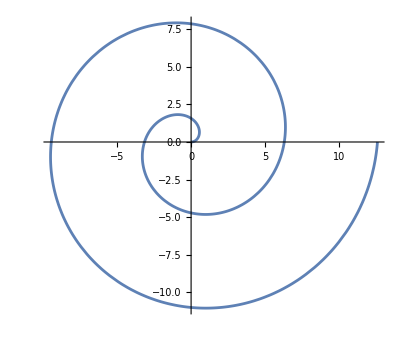

```mathematica
ParametricPlot[{t*Cos[t], t*Sin[t]},{t,0,4*Pi}]
```

ContourPlot

https://reference.wolfram.com/language/ref/ContourPlot.html?q=ContourPlot

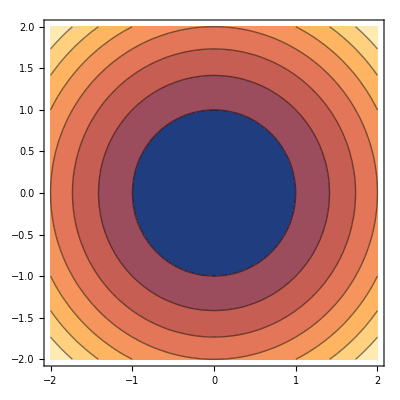

```mathematica
ContourPlot[x^2+y^2,{x,-2,2},{y,-2,2}]
```

Plot

https://reference.wolfram.com/language/ref/Plot.html

```mathematica
Plot[f[t],{t,-1,4}]
```

-Graphics-

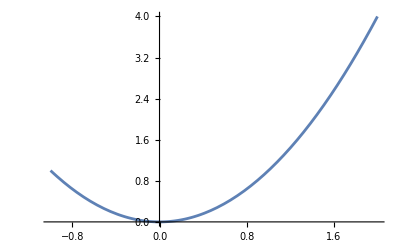

```mathematica
Plot[x^2,{x,-1,2}]
```

Function

https://reference.wolfram.com/language/ref/Function.html

```mathematica
f1 = Function[{x},x^2]
f1[25]
```

Function[{x},x^2]

625

```mathematica
f2 = #^2&
```

#1^2&

```mathematica
g = #2+#1*#2&   (* 匿名函数表示 g(x,y)=y+xy *)
```

#2+#1 #2&

```mathematica
g[2,5]
```

15

Input

https://reference.wolfram.com/language/ref/Input.html?q=Input

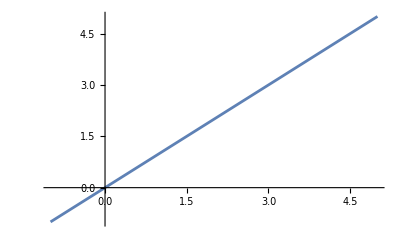

```mathematica
f = Input[];
Plot[f,{x,-1,5}]
```

Export

https://reference.wolfram.com/language/ref/Export.html?q=Export

```mathematica
(* Export["path", 2+3, ".JSON"]
  Export["path", Plot[x^2,{x,-1,3},ImageSize->1000],"png"]	
*)
```

D

https://reference.wolfram.com/language/ref/D.html?q=D

```mathematica
f[x_, y_] := x^2 + y^2 
f[3, 4]
D[f[x,y],{x,1}]
```

25

2 x

终止操作

alt + .

while

https://reference.wolfram.com/language/ref/While.html